```mathematica
ClearAll[MySimplify,σ3Simplify,TraceSimplify,FinalSimplify,Para,Perp,commutationRules,rule]
rule = {Tr[Subscript[σ, 3]]->0,Tr[Π[0]]->0,Tr[Π[0].Subscript[σ, 3]]->0,Tr[Subscript[σ, 3].Π[0]]->0,Tr[Id]->0,Tr[1]->0,Tr[0]->0,Tr[Der[x_]]->0,Tr[Der[x_].Subscript[σ, 3]]->0,Tr[Subscript[σ, 3].Der[x_]]->0};
commutationRules={Subscript[σ, 3].Subscript[σ, 3]:>1,1 .x_:>x,x_ . 1:>x,Tr[x___ .minus.y___]:>-Tr[x.y],Tr[Subscript[σ, 3].(rest___)]/;!MatchQ[{rest},{Subscript[σ, 3],___}]:>Tr[rest.Subscript[σ, 3]],Subscript[σ, 3].Π[arg_]:>Π[arg].Subscript[σ, 3],Subscript[σ, 3].Der[arg_]:>Der[arg].Subscript[σ, 3],Subscript[σ, 3].Para[any_]:>Para[any].Subscript[σ, 3],Subscript[σ, 3].Perp[any_]:>minus.Perp[any].Subscript[σ, 3]};


Para[Perp[x_]]:=0;
Perp[Para[x_]]:=0;
Para[Para[x_]]:=Para[x];
Perp[Perp[x_]]:=Perp[x];
Para[Der[x_]]:=Der[x];
Perp[Der[x_]]:=0;
Para[Π[x_]]:=Π[x];
Perp[Π[x_]]:=0;
Para[Subscript[σ, 3]]:=Subscript[σ, 3];
Perp[Subscript[σ, 3]]:=0;
Para[Id]:=1;
Perp[Id]:=0;
Para[1]:=1;
Perp[1]:=0;
(*Para[Φ[x_]]:=0;
Perp[Φ[x_]]:=Φ[x];*)
Para[x_ .y_]:=Para[x].Para[y]+Perp[x].Perp[y];
Perp[x_ .y_]:=Para[x].Perp[y]+Perp[x].Para[y];
Para[0]:=0;
Perp[0]:=0;

MySimplify[A_ + B_]:=MySimplify[A]+MySimplify[B];
MySimplify[A_ B_]:=MySimplify[A]MySimplify[B];
MySimplify[A_]:=A;
MySimplify[Tr[x_]]:= σ3Simplify[Tr[x]];

σ3Simplify[expr_]:=expr//.commutationRules;

TraceSimplify[x_ y_]:=TraceSimplify[x]TraceSimplify[y];
TraceSimplify[x_^n_]:=(TraceSimplify[x])^n;
TraceSimplify[x_ +y_]:=TraceSimplify[x]+TraceSimplify[y];
TraceSimplify[Tr[x_ + y_]]:= TraceSimplify[Tr[x]]+TraceSimplify[Tr[y]];
TraceSimplify[Tr[x___ .Π[0].y___]]=TraceSimplify[Tr[x.y]]Ð[0];
TraceSimplify[Tr[x_]]:= MySimplify[Tr[x]];
TraceSimplify[x_?NumericQ]:=x;
TraceSimplify[λ]=λ;
TraceSimplify[λ^n_]:=λ^n;
TraceSimplify[t]:=t;
TraceSimplify[t^n_]:=t^n;
TraceSimplify[ν0]:=ν0;
TraceSimplify[ν0^n_]:=ν0^n;
TraceSimplify[Dp]:=Dp;
TraceSimplify[Dp^n_]:=Dp^n;
TraceSimplify[Ð[0]]:=Ð[0];
TraceSimplify[Ð[0]^n_]:=Ð[0]^n;

cycleΦtoFirst[x_ y_]:=cycleΦtoFirst[x]cycleΦtoFirst[y];
cycleΦtoFirst[x_^n_]:=(cycleΦtoFirst[x])^n;
cycleΦtoFirst[x_ +y_]:=cycleΦtoFirst[x]+cycleΦtoFirst[y];
cycleΦtoFirst[Tr[x___.Φ[a_].y___]]:=Tr[Φ[a].y.x];
cycleΦtoFirst[Tr[x_]]:=Tr[x];
cycleΦtoFirst[x_?NumericQ]:=x;
cycleΦtoFirst[t]:=t;
cycleΦtoFirst[t^n_]:=t^n;
cycleΦtoFirst[λ]:=λ;
cycleΦtoFirst[λ^n_]:=λ^n;
cycleΦtoFirst[ν0]:=ν0;
cycleΦtoFirst[ν0^n_]:=ν0^n;
cycleΦtoFirst[Dp]:=Dp;
cycleΦtoFirst[Dp^n_]:=Dp^n;
cycleΦtoFirst[Ð[0]]:=Ð[0];
cycleΦtoFirst[Ð[0]^n_]:=Ð[0]^n;

FinalSimplify[x_]:=((cycleΦtoFirst[TraceSimplify[TensorExpand[x]]])//.rule)//FullSimplify;
```

```mathematica
(*---0. LISP INTERFACE---*)
EvaluateModel[lispCommand_String]:=Module[{scriptPath,sbclPath,processResult,rawOutput,cleanString,data},(*1. PATH CONFIGURATION*)(*Update these paths to match your system*)scriptPath="/Users/zjitu/Documents/Lisp/NLSM/nlsm.lisp";
sbclPath="/opt/homebrew/bin/sbcl";
(*2. EXECUTE LISP (Corrected)*)(*We do NOT ask for "StandardOutput" here,so we get the full status object*)processResult=RunProcess[{sbclPath,"--script",scriptPath,lispCommand}];
(*3. ERROR CHECKING*)If[processResult["ExitCode"]=!=0,Print["Lisp Script Failed!"];
Print[processResult["StandardError"]];
Return[$Failed];];
rawOutput=processResult["StandardOutput"];
(*4. SMART EXTRACTION*)(*Extracts only the Association <|...|>,ignoring NILs or warnings*)cleanString=First[StringCases[rawOutput,"<|"~~___~~"|>"],"" (*Fallback*)];
If[cleanString==="",Print["Extraction Failed. No valid Association found in output."];
Print["Raw Output: ",rawOutput];
Return[$Failed];];
(*5. CONVERT TO CODE*)data=ToExpression[cleanString];
Return[data];];
```

```mathematica
(*---1. CONFIGURATION& STYLES---*)$HubBaseRadius=0.01;
$HubGrowthFactor=0.25;
$RibbonWidthOuter=0.08;
$RibbonWidthInner=0.06;
$HashWidth=0.55;

(*Function:getNormal Description:Calculates the 2D normal vector perpendicular to a given tangent.Input:tangent (List of 2 coordinates).Output:List of 2 coordinates representing the normal vector.*)
getNormal[tangent_]:={-tangent[[2]],tangent[[1]]}/Norm[tangent];

(*---2. DRAWING PRIMITIVES---*)

(*Function:drawRibbonCurve Description:Renders a black-and-white double Bezier curve for standard propagators.Input:p1,c1,c2,p2 (Control points of the Bezier curve).Output:List of graphics primitives.*)
drawRibbonCurve[p1_,c1_,c2_,p2_]:={Black,Thickness[$RibbonWidthOuter],CapForm["Round"],BezierCurve[{p1,c1,c2,p2}],White,Thickness[$RibbonWidthInner],CapForm["Round"],BezierCurve[{p1,c1,c2,p2}]};

(*Function:drawRedRibbonCurve Description:Renders a red-and-white double Bezier curve for external fields.Input:p1,c1,c2,p2 (Control points of the Bezier curve).Output:List of graphics primitives.*)
drawRedRibbonCurve[p1_,c1_,c2_,p2_]:={Red,Thickness[$RibbonWidthOuter],CapForm["Round"],BezierCurve[{p1,c1,c2,p2}],White,Thickness[$RibbonWidthInner],CapForm["Round"],BezierCurve[{p1,c1,c2,p2}]};

(*Function:drawTripleHash Description:Draws the triple-line hash mark used to denote contractions.Input:mid (Center position),tangent (Direction vector of the tube at midpoint).Output:List of graphics primitives (Line objects).*)
drawTripleHash[mid_,tangent_]:=Module[{norm,spacing},norm=getNormal[tangent];
spacing=0.09;
{Black,Thickness[0.012],CapForm["Butt"],Line[{mid-norm*$HashWidth/2,mid+norm*$HashWidth/2}],Line[{mid-norm*$HashWidth/2-tangent*spacing,mid+norm*$HashWidth/2-tangent*spacing}],Line[{mid-norm*$HashWidth/2+tangent*spacing,mid+norm*$HashWidth/2+tangent*spacing}]}];

(*Function:drawPhi Description:Draws the external field symbol (Phi) as a split ribbon.Input:pos (Attachment point on the hub),normal (Outward normal vector).Output:List of graphics primitives.*)
drawPhi[pos_,normal_]:=Module[{splitLen=0.7,spread=0.6,tip1,tip2,c1,root},root=pos-normal*0.05;
tip1=pos+normal*splitLen+{-normal[[2]],normal[[1]]}*spread;
tip2=pos+normal*splitLen-{-normal[[2]],normal[[1]]}*spread;
c1=pos+normal*(splitLen*0.3);
{drawRedRibbonCurve[root,c1,tip1,tip1],drawRedRibbonCurve[root,c1,tip2,tip2]}];

(*Function:drawHub Description:Draws the central interaction vertex (white disk).Input:center (2D coordinates),radius (Radius of the disk).Output:List of graphics primitives.*)
drawHub[center_,radius_]:={FaceForm[White],EdgeForm[{Black,Thickness[0.01]}],Disk[center,radius]};

(*---3. PARSING& ASSEMBLING---*)

(*Function:getPortCoords Description:Calculates the absolute coordinates for a port on a hub's perimeter.Input:center (Hub center),n (Total ports),i (Index of current port),radius.Output:List of 2 coordinates.*)
getPortCoords[center_,n_,i_,radius_]:=Module[{angle},angle=135 Degree-(360 Degree*(i-1))/n;
center+radius*{Cos[angle],Sin[angle]}];

(*Function:getPortNormal Description:Calculates the normal vector pointing outward from a specific port.Input:n (Total ports),i (Index of current port).Output:List of 2 coordinates.*)
getPortNormal[n_,i_]:=Module[{angle},angle=135 Degree-(360 Degree*(i-1))/n;
{Cos[angle],Sin[angle]}];

(*Function:extractPos Description:Extracts the spatial position from an expression,robust to'W' wrappers with multiple args.Input:arg (The expression segment).Output:The position symbol (e.g.,X,Y) or the argument itself if no wrapper found.*)
extractPos[arg_]:=Module[{found},If[MatchQ[arg,_Symbol|_Integer|_Plus|_Subtract],Return[arg]];
(*Updated pattern W[p_,___] to ignore extra arguments like Der[...]*)found=FirstCase[arg,W[p_,___]:>p,None,Infinity];
If[found=!=None,Return[found]];
arg];

(*Function:parseSkeleton Description:Scans the skeleton expression to identify interaction vertices and external fields.Input:expr (The skeleton expression).Output:Association mapping Position->List of Operations.*)
parseSkeleton[expr_]:=Module[{wOps,phiOps,allOps},(*Updated pattern to handle Tagged[id,W[pos,extra...]]*)wOps=Cases[expr,Tagged[id_,W[pos_,___]]:><|"Type"->"W","ID"->id,"Pos"->pos|>,Infinity];
phiOps=Cases[expr,(Phi|Φ)[arg_]:><|"Type"->"Phi","ID"->"Phi_"<>ToString[Unique[]],"Pos"->extractPos[arg]|>,Infinity];
allOps=Join[wOps,phiOps];
GroupBy[allOps,#Pos&]];

(*Function:drawSmartTube Description:routes a propagator tube between two points,applying detour logic to avoid collision.Input:p1,n1 (Start point/normal),p2,n2 (End point/normal).Output:List containing {TubeGraphics,HashGraphics}.*)
drawSmartTube[p1_,n1_,p2_,n2_]:=Module[{dist,c1,c2,mid,tangent,curve,sumN,detourVector},dist=EuclideanDistance[p1,p2];
c1=p1+n1*2.5;
c2=p2+n2*2.5;
sumN=n1+n2;
If[Norm[sumN]<0.5,detourVector=Normalize[{-(p2[[2]]-p1[[2]]),(p2[[1]]-p1[[1]])}];
If[detourVector.n1<0,detourVector=-detourVector];
c1=c1+detourVector*3.0;
c2=c2+detourVector*3.0;,If[dist>2.0,c1=p1+n1*(1.5+dist*0.8);
c2=p2+n2*(1.5+dist*0.8);];];
curve=BezierFunction[{p1,c1,c2,p2}];
mid=curve[0.5];
tangent=Normalize[curve'[0.5]];
{drawRibbonCurve[p1,c1,c2,p2],drawTripleHash[mid,tangent]}];

(*Function:drawDiagram Description:Main assembly function.Positions hubs,draws ports,and routes connections based on topology.Input:skeleton (Expression),topology (List of ID pairs).Output:Graphics object containing the full diagram.*)
drawDiagram[skeleton_,topology_]:=Module[{blocksData,distinctPos,posMap,layerTubes,layerHubs,layerHashes,globalPortMap,blockCenter,ops,nPorts,radius,coord,norm,p1,n1,p2,n2,id1,id2,tubes,hash},blocksData=parseSkeleton[skeleton];
distinctPos=Keys[blocksData];
posMap=AssociationThread[distinctPos->Table[{i*6.0,0},{i,0,Length[distinctPos]-1}]];
layerTubes={};layerHubs={};layerHashes={};
globalPortMap=<||>;
Do[blockCenter=posMap[pos];
ops=blocksData[pos];
nPorts=Length[ops];
radius=$HubBaseRadius+(nPorts*$HubGrowthFactor);
AppendTo[layerHubs,drawHub[blockCenter,radius]];
Do[coord=getPortCoords[blockCenter,nPorts,i,radius];
norm=getPortNormal[nPorts,i];
op=ops[[i]];
If[op["Type"]=="Phi",AppendTo[layerTubes,drawPhi[coord,norm]]];
If[op["Type"]=="W",globalPortMap[op["ID"]]={coord,norm}];,{i,1,nPorts}];,{pos,distinctPos}];
Do[id1=pair[[1]];id2=pair[[2]];
If[KeyExistsQ[globalPortMap,id1]&&KeyExistsQ[globalPortMap,id2],p1=globalPortMap[id1][[1]];
n1=globalPortMap[id1][[2]];
p2=globalPortMap[id2][[1]];n2=globalPortMap[id2][[2]];
{tubes,hash}=drawSmartTube[p1,n1,p2,n2];
AppendTo[layerTubes,tubes];
AppendTo[layerHashes,hash];];,{pair,topology}];
Graphics[{layerHubs,layerTubes,layerHashes},ImageSize->{Automatic,200},Background->None,PlotRange->All]];

(*---4. REPORT GENERATOR (REFINED)---*)(*Function:cleanSkeletonDisplay Description:Reformats the skeleton for beautiful printing.-Tagged[id,content]->content-Der[x]->Subscript[∇,x] (Visual only)-W[pos,extra]->extra.W[pos]*)cleanSkeletonDisplay[expr_]:=expr//. {(*Rule 1:Remove Tagged wrapper*)Tagged[_,content_]:>content,(*Rule 2:Convert Der[x] to Subscript[Del,x] We use the string "∇" to avoid conflict with the built-in Del operator*)Der[x_]:>Subscript["∇",x],(*Rule 3:Reorder W so derivative comes first:Der[Y].W[Y]*)W[pos_,extra_]:>Dot[extra,W[pos]]};

(*Function:generateReport Description:Generates the grid with the refined equation header.*)
generateReport[data_,factor_:1]:=Module[{skeleton,cleanedSkeleton,diagrams,gridItems,headerRow,titleRow},skeleton=data["Skeleton"];
diagrams=data["Diagrams"];
(*Apply the cleaning logic*)cleanedSkeleton=cleanSkeletonDisplay[skeleton];
(*Create Diagram Rows*)gridItems=Table[{Style[diag["ID"],20,Bold],drawDiagram[skeleton,diag["Topology"]],Pane[FinalSimplify[factor*diag["Value"]],{350,Automatic},ImageSizeAction->"Scrollable"]},{diag,diagrams}];
headerRow={Style["ID",Bold],Style["Diagram",Bold],Style["Value",Bold]};
(*Title Row:Displays the formatted equation*)titleRow={Item[Style[TraditionalForm[cleanedSkeleton],20,Black],Background->LightBlue,Frame->True,Alignment->Center],SpanFromLeft,SpanFromLeft};
Grid[Join[{titleRow,headerRow},gridItems],Frame->All,Spacings->{1,1},ItemStyle->{{Left,Center,Left}},Alignment->{Left,Center}]];


(*---5. FINAL EXPORT UTILITIES---*)
(*Function:saveReport Description:Saves the summary report to the EXACT path you specify.No IDs are appended.Example:Input path:"report/S2p_a.pdf" Output:"report/S2p_a.pdf"*)
saveReport[data_,path_,factor_:1]:=Module[{reportGrid,dir},(*1. Ensure directory exists*)dir=DirectoryName[path];
If[dir=!=""&&!DirectoryQ[dir],CreateDirectory[dir]];
(*2. Generate and Export exactly to'path'*)reportGrid=generateReport[data,factor];
Export[path,reportGrid];
Print["Report saved successfully to: ",path];
path];
```

```mathematica
(*



Begining of Report!



*)
```

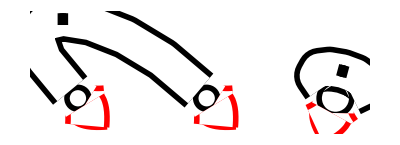
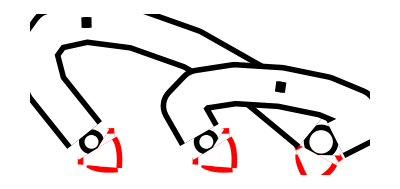
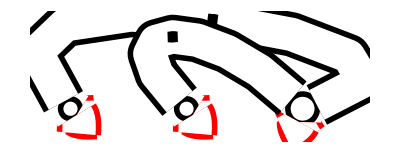
Tr[Φ(X).∇_X .W(X)].Tr[Φ(Y).∇_Y .W(Y)].Tr[Φ(Z).W(Z).W(Z)] |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | 1/4 t^2 Tr[Perp[Φ[Y]].Der[Y].Π[Y-Z].Para[Φ[Z]].Perp[Φ[X]].Der[X].Π[X-Z]]
3 | -Graphics- | 1/4 t^2 Tr[Perp[Φ[Y]].Der[Y].Π[Y-Z].Perp[Φ[X]].Der[X].Π[X-Z].Para[Φ[Z]]]

```mathematica
(*TEST*)
data=EvaluateModel["(main '(* (tr (Phi x)  (W x (d x))) (tr (Phi y)  (W y (d y))) (tr (Phi z) (W z) (W z))))"];
generateReport[data]
```

```mathematica
(*



Try: Calculation of 2-loop RG for non-interacting NLSM! 




*)
```

Report saved successfully to: report/S2p_a.pdf

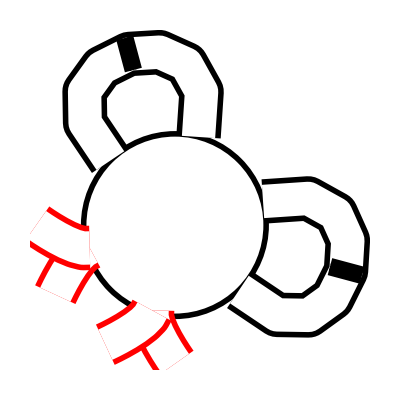
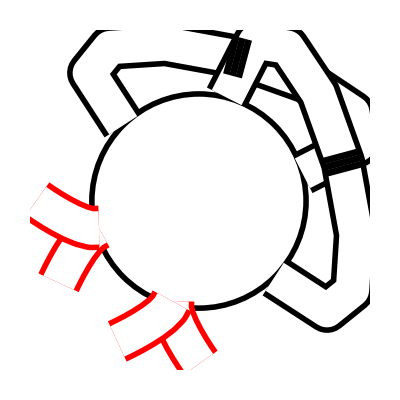
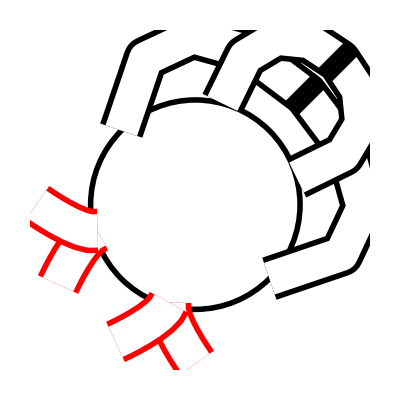
Tr[Φ(R).σ_3.W(R).W(R).Φ(R).σ_3.W(R).W(R)] |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | -1/8 t Ð[0]^2 Tr[Perp[Φ[R]].Perp[Φ[R]]]
3 | -Graphics- | 0

```mathematica
(*1. Ensure paths are relative to this Notebook's location*)
SetDirectory[NotebookDirectory[]];
pathReport="report/S2p_a.pdf";

factor=1/(2 t);
data=EvaluateModel["(main '(* (tr (Phi r) Sigma3 (W r) (W r) (Phi r) Sigma3 (W r) (W r))))"];
saveReport[data,pathReport,factor];
generateReport[data,factor]
```

```mathematica
SetDirectory[NotebookDirectory[]];
pathReport="report/S2p_b.pdf";

factor=λ/(2 t);
data=EvaluateModel["(main '(* (tr (Phi r) Sigma3 (Phi r) Sigma3 (W r) (W r) (W r) (W r))))"];
saveReport[data,pathReport,factor];
generateReport[data,factor]
```

Report saved successfully to: report/S2p_b.pdf

Tr[Φ(R).σ_3.Φ(R).σ_3.W(R).W(R).W(R).W(R)] |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | 0
3 | -Graphics- | 0

```mathematica
SetDirectory[NotebookDirectory[]];
pathReport="report/S2p_c.pdf";

factor=(1+λ)/(2 t);
data=EvaluateModel["(main '(* (tr (Phi r) Sigma3 (W r) (Phi r) Sigma3 (W r) (W r) (W r))))"];
saveReport[data,pathReport,factor];
generateReport[data,factor]
```

Report saved successfully to: report/S2p_c.pdf

Tr[Φ(R).σ_3.W(R).Φ(R).σ_3.W(R).W(R).W(R)] |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | 0
3 | -Graphics- | 0

Report saved successfully to: report/S1squared_11.pdf

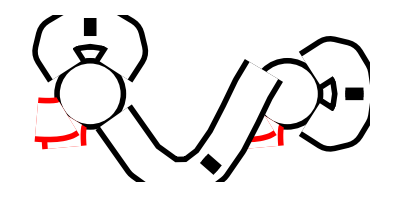
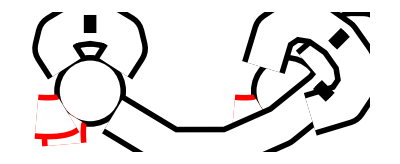
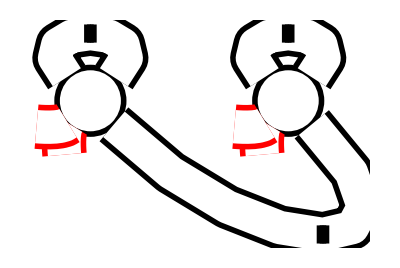
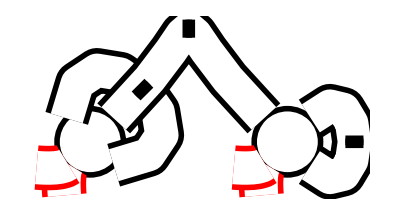
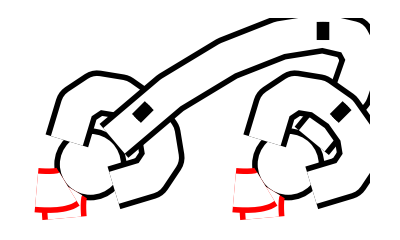
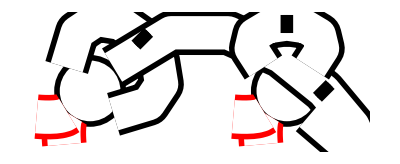
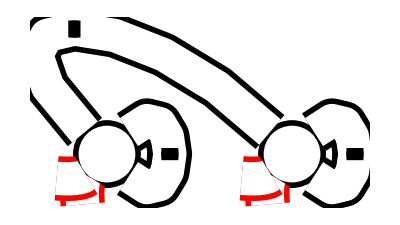
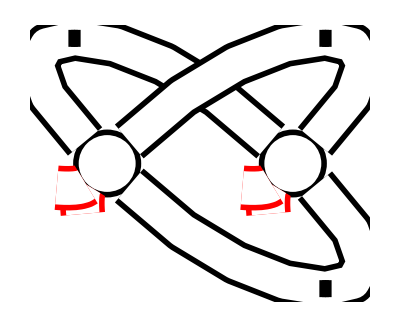
Tr[Φ(X).∇_X .W(X).W(X).W(X)].Tr[Φ(Y).∇_Y .W(Y).W(Y).W(Y)] |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | 0
3 | -Graphics- | 0
4 | -Graphics- | 0
5 | -Graphics- | 0
6 | -Graphics- | 0
7 | -Graphics- | 0
8 | -Graphics- | 1/64 t (1+λ)^2 Tr[Perp[Φ[X]].Der[X].Der[Y].Π[X-Y].Π[X-Y].Π[X-Y].Perp[Φ[Y]]]
9 | -Graphics- | 0
10 | -Graphics- | 0
11 | -Graphics- | 0
12 | -Graphics- | 0
13 | -Graphics- | 0
14 | -Graphics- | 0
15 | -Graphics- | 0

```mathematica
SetDirectory[NotebookDirectory[]];
pathReport="report/S1squared_11.pdf";

factor=-(1+λ)^2/(8 t^2);
data=EvaluateModel["(main '(* (tr (Phi x) (W x (d x)) (W x) (W x)) (tr (Phi y) (W y (d y)) (W y) (W y))))"];
saveReport[data,pathReport,factor];
generateReport[data,factor]
```

```mathematica
SetDirectory[NotebookDirectory[]];
pathReport="report/S1squared_13.pdf";

factor=-(1+λ)^2/(8 t^2);
data=EvaluateModel["(main '(* (tr (Phi x) (W x (d x)) (W x) (W x)) (tr (Phi y) (W y) (W y) (W y (d y)))))"];
saveReport[data,pathReport,factor];
generateReport[data,factor]
```

Report saved successfully to: report/S1squared_13.pdf

Tr[Φ(X).∇_X .W(X).W(X).W(X)].Tr[Φ(Y).W(Y).W(Y).∇_Y .W(Y)] |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | 0
3 | -Graphics- | 0
4 | -Graphics- | 0
5 | -Graphics- | 0
6 | -Graphics- | 0
7 | -Graphics- | 0
8 | -Graphics- | 1/64 t (1+λ)^2 Tr[Perp[Φ[X]].Der[X].Π[X-Y].Π[X-Y].Der[Y].Π[X-Y].Perp[Φ[Y]]]
9 | -Graphics- | 0
10 | -Graphics- | 0
11 | -Graphics- | 0
12 | -Graphics- | 0
13 | -Graphics- | 0
14 | -Graphics- | 0
15 | -Graphics- | 0

```mathematica
SetDirectory[NotebookDirectory[]];
pathReport="report/S1squared_31.pdf";

factor=-(1+λ)^2/(8 t^2);
data=EvaluateModel["(main '(* (tr (Phi x) (W x) (W x) (W x (d x))) (tr (Phi y) (W y (d y)) (W y) (W y))))"];
saveReport[data,pathReport,factor];
generateReport[data,factor]
```

Report saved successfully to: report/S1squared_31.pdf

Tr[Φ(X).W(X).W(X).∇_X .W(X)].Tr[Φ(Y).∇_Y .W(Y).W(Y).W(Y)] |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | 0
3 | -Graphics- | 0
4 | -Graphics- | 0
5 | -Graphics- | 0
6 | -Graphics- | 0
7 | -Graphics- | 0
8 | -Graphics- | 1/64 t (1+λ)^2 Tr[Perp[Φ[X]].Der[Y].Π[X-Y].Π[X-Y].Der[X].Π[X-Y].Perp[Φ[Y]]]
9 | -Graphics- | 0
10 | -Graphics- | 0
11 | -Graphics- | 0
12 | -Graphics- | 0
13 | -Graphics- | 0
14 | -Graphics- | 0
15 | -Graphics- | 0

```mathematica
SetDirectory[NotebookDirectory[]];
pathReport="report/S1squared_33.pdf";

factor=-(1+λ)^2/(8 t^2);
data=EvaluateModel["(main '(* (tr (Phi x) (W x) (W x) (W x (d x))) (tr (Phi y) (W y) (W y) (W y (d y)))))"];
saveReport[data,pathReport,factor];
generateReport[data,factor]
```

Report saved successfully to: report/S1squared_33.pdf

Tr[Φ(X).W(X).W(X).∇_X .W(X)].Tr[Φ(Y).W(Y).W(Y).∇_Y .W(Y)] |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | 0
3 | -Graphics- | 0
4 | -Graphics- | 0
5 | -Graphics- | 0
6 | -Graphics- | 0
7 | -Graphics- | 0
8 | -Graphics- | 1/64 t (1+λ)^2 Tr[Perp[Φ[X]].Π[X-Y].Π[X-Y].Der[X].Der[Y].Π[X-Y].Perp[Φ[Y]]]
9 | -Graphics- | 0
10 | -Graphics- | 0
11 | -Graphics- | 0
12 | -Graphics- | 0
13 | -Graphics- | 0
14 | -Graphics- | 0
15 | -Graphics- | 0

Report saved successfully to: report/S0pS2_13.pdf

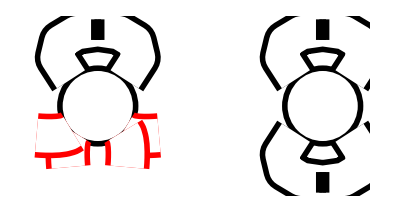
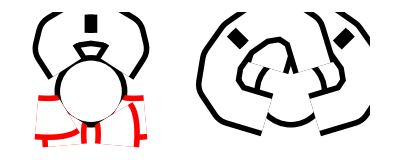
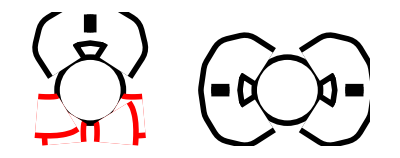
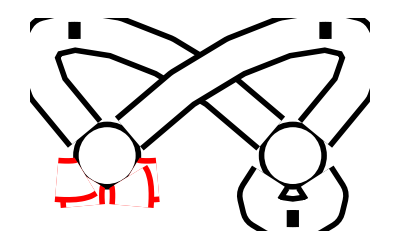
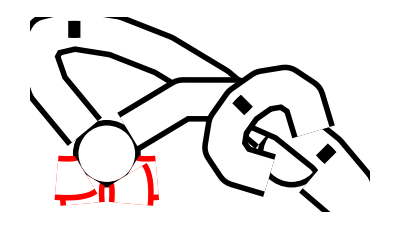
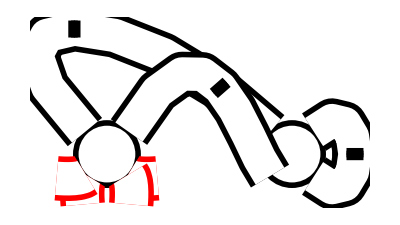
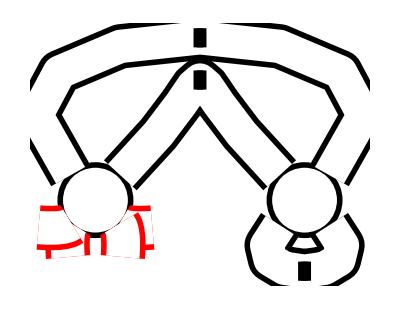
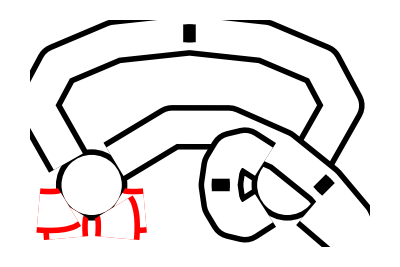
Tr[Φ(X).σ_3.Φ(X).σ_3.W(X).W(X)].Tr[∇_Y .W(Y).W(Y).∇_Y .W(Y).W(Y)] |  | 
ID | Diagram | Value
1 | -Graphics- | 0
2 | -Graphics- | 0
3 | -Graphics- | 0
4 | -Graphics- | 0
5 | -Graphics- | 0
6 | -Graphics- | 0
7 | -Graphics- | 0
8 | -Graphics- | 0
9 | -Graphics- | 0
10 | -Graphics- | 0
11 | -Graphics- | 0
12 | -Graphics- | 0
13 | -Graphics- | 0
14 | -Graphics- | 0
15 | -Graphics- | 0

```mathematica
SetDirectory[NotebookDirectory[]];
pathReport="report/S0pS2_13.pdf";

factor=-(1-λ)/(2 t^2);
data=EvaluateModel["(main '(* (tr (Phi x) sigma3 (Phi x) sigma3 (W x) (W x)) (tr (W y (d y)) (W y) (W y (d y)) (W y))))"];
saveReport[data,pathReport,factor];
generateReport[data,factor]
```

Report saved successfully to: report/RG_1_TEST.pdf

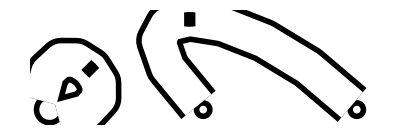
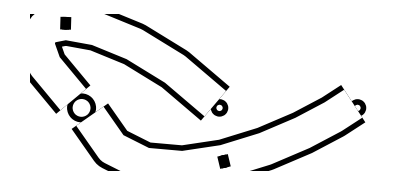
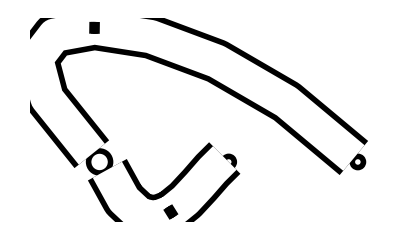
Tr[Ε.∇_X .W(X).∇_X .W(X)].Tr[ϕ(Y).σ_3.W(Y)].Tr[ϕ(Z).σ_3.W(Z)] |  | 
ID | Diagram | Value
1 | -Graphics- | 1/8 ⅈ π t^2 cycleΦtoFirst[TraceSimplify[Dp]] cycleΦtoFirst[TraceSimplify[ν]] Ð[0] Tr[Perp[ϕ[Y]].Π[Y-Z].Perp[ϕ[Z]]] (-Tr[Para[Ε].σ_3] Tr[Der[X].Der[X].σ_3]+Tr[Der[X].Der[X]] Tr[Para[Ε]])
2 | -Graphics- | 1/4 ⅈ π t^2 cycleΦtoFirst[TraceSimplify[Dp]] cycleΦtoFirst[TraceSimplify[ν]] Tr[Para[Ε].Der[X].Π[X-Y].Perp[ϕ[Y]].Der[X].Π[X-Z].Perp[ϕ[Z]]]
3 | -Graphics- | 1/4 ⅈ π t^2 cycleΦtoFirst[TraceSimplify[Dp]] cycleΦtoFirst[TraceSimplify[ν]] Tr[Para[Ε].Der[X].Π[X-Z].Perp[ϕ[Z]].Der[X].Π[X-Y].Perp[ϕ[Y]]]

```mathematica
SetDirectory[NotebookDirectory[]];
pathReport="report/RG_1_TEST.pdf";

factor=-ⅈ π ν Dp;
data=EvaluateModel["(main '(* (tr UbarEU (W x (d x)) (W x (d x))) (tr (varphi y) sigma3 (W y)) (tr (varphi z) sigma3 (W z))))"];
saveReport[data,pathReport,factor];
generateReport[data,factor]
```